```mathematica
SetDirectory[NotebookDirectory[]]
```

/media/george/Almacenamiento1/Storage/8-Momentum Transfer from electrons to NPs/FFTW

```mathematica
reGauss=Import["fftw_output_re.txt","Data"];
imGauss=Import["fftw_output_im.txt","Data"];
```

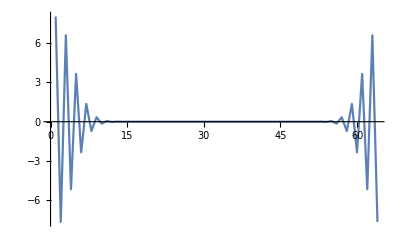

```mathematica
ListPlot[reGauss, Joined->True, PlotRange->All]
```

```mathematica
NN=2^6
Fourier[Table[Cos[3*2*π*i/NN],{i,0,NN-1}]]//Chop
```

64

{0,0,0,4.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4.,0,0}

```mathematica
exp(-0.5*pow((t-t0)/sigma,2.0))
```

```mathematica
NN=2^6
listGaussian=Fourier[Table[√NN Exp[-0.5 * (-10+20*i/NN)^2],{i,0,NN-1}]]//Chop
```

64

{8.02121,-7.63499,6.58436,-5.14465,3.64196,-2.33588,1.35739,-0.714649,0.340894,-0.147327,0.0576876,-0.0204654,0.00657799,-0.0019156,0.000505419,-0.000120819,0.0000261672,-5.1347×10^-6,9.12872×10^-7,-1.47042×10^-7,2.1459×10^-8,-2.83737×10^-9,3.39905×10^-10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3.39905×10^-10,-2.83737×10^-9,2.1459×10^-8,-1.47042×10^-7,9.12872×10^-7,-5.1347×10^-6,0.0000261672,-0.000120819,0.000505419,-0.0019156,0.00657799,-0.0204654,0.0576876,-0.147327,0.340894,-0.714649,1.35739,-2.33588,3.64196,-5.14465,6.58436,-7.63499}

```mathematica
Length[listGaussian]
```

64

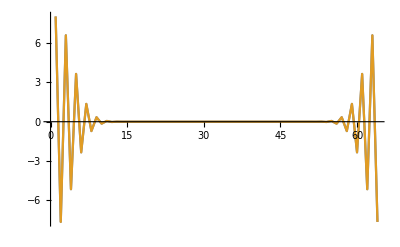

```mathematica
ListPlot[{listGaussian, reGauss}, Joined->True, PlotRange->All]
```

```mathematica
FourierTransform[Cos[3*t],t,ω]
```

√(π/2) DiracDelta[-3+ω]+√(π/2) DiracDelta[3+ω]

```mathematica
1/√32.
```

0.176777